```mathematica
NS["study_overlearning_180705"]
```

```mathematica
expsum=Table[Exp[t*s],{s,0,2}]
```

{1,ⅇ^t,ⅇ^(2 t)}

```mathematica
z=Total@expsum
```

1+ⅇ^t+ⅇ^(2 t)

```mathematica
prob=expsum/z
```

{1/(1+ⅇ^t+ⅇ^(2 t)),ⅇ^t/(1+ⅇ^t+ⅇ^(2 t)),ⅇ^(2 t)/(1+ⅇ^t+ⅇ^(2 t))}

```mathematica
arr=Flatten[{Array[a,{3,2}],Array[b,2]}]
```

{a[1,1],a[1,2],a[2,1],a[2,2],a[3,1],a[3,2],b[1],b[2]}

```mathematica
finpoints=T[{{0,0},{1/2,Sqrt[3]/2},{1,0}}]
```

{{0,1/2,1},{0,(√3)/2,0}}

```mathematica
(Array[a,{2,3}].T[{{1,0,0},{0,1,0},{0,0,1}}]+Array[b,2])//MF
```

(a[1,1]+b[1] | a[1,2]+b[1] | a[1,3]+b[1]
a[2,1]+b[2] | a[2,2]+b[2] | a[2,3]+b[2])

```mathematica
FS@Solve[Array[a,{2,3}].T[{{1,0,0},{0,1,0},{0,0,1}}]+Array[b,2]==T@{{0,0},{1,0},{1/2,Sqrt[3]/2}},arr]
```

{{a[1,1]→-1/2+a[1,3],a[1,2]→1/2+a[1,3],a[2,1]→-(√3)/2+a[2,3],a[2,2]→-(√3)/2+a[2,3],b[1]→1/2-a[1,3],b[2]→1/2 (√3-2 a[2,3])}}

```mathematica
ParametricPlot[finpoints.prob,{t,-100,100},PlotRange->{{0,1},{0,Sqrt[3]/2}},AspectRatio->Auto]
```

```mathematica
subs=Assuming[0<m<2,FS@Solve[{0,1,2}.prob==m,t,Reals]][[1]]
```

{t→-Log[4-2 m]+Log[-1+m+√(1-3 (-2+m) m)]}

```mathematica
probm=Assuming[0<m<2,FS[prob/.subs]]
```

{1/6 (7-3 m-√(1-3 (-2+m) m)),1/3 (-1+√(1-3 (-2+m) m)),1/6 (1+3 m-√(1-3 (-2+m) m))}

```mathematica
triangle=Graphics[{Thick,green,Line[T[finpoints.T[{{1,0,0},{0,1,0},{0,0,1},{1,0,0}}]]]}];
```

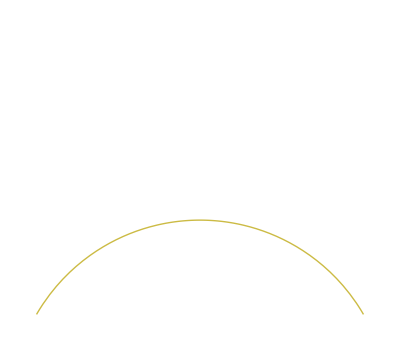

```mathematica
parplot=ParametricPlot[finpoints.probm,{m,0,2},PlotStyle->{Thick,yellow},PlotRange->{{0,1},{0,Sqrt[3]/2}},AspectRatio->Auto,Axes->None]
```

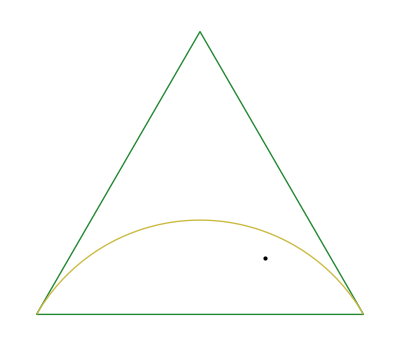

```mathematica
freq={2/10,2/10,1-4/10};Show[{triangle,parplot,Graphics@Point[finpoints.freq]}]
```

```mathematica
nobs=15;data=RandomChoice[freq->{1,2,3},nobs];
```

```mathematica
nsamples=25;
updens[0]=FS[(m-1)^4/Integrate[(m-1)^4,{m,0,2}]];
upprob[0]=FS@NIntegrate[probm*updens[0],{m,0,2}];
```

```mathematica
Do[
datas=RandomSample[data];
updens[sample,0]=updens[0];
upprob[sample,0]=upprob[0];
Do[Print[sample," -",i];updens[sample,i]=Assuming[0<m<2,FS[probm[[datas[[i]]]]*updens[sample,i-1]/NIntegrate[probm[[datas[[i]]]]*updens[sample,i-1],{m,0,2}]]];
upprob[sample,i]=FS@NIntegrate[probm*updens[sample,i],{m,0,2}],{i,1,nobs}];,{sample,1,nsamples}];
```

```mathematica
Do[upprob[i]=Mean[Table[upprob[sample,i],{sample,nsamples}]],{i,nobs}];{upprob[nobs],freq}//N//MF
```

(0.107483 | 0.252758 | 0.639759
0.2 | 0.2 | 0.6)

```mathematica
Table[upprob[samples,nobs],{samples,8}]//MF
```

(0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759
0.107483 | 0.252758 | 0.639759)

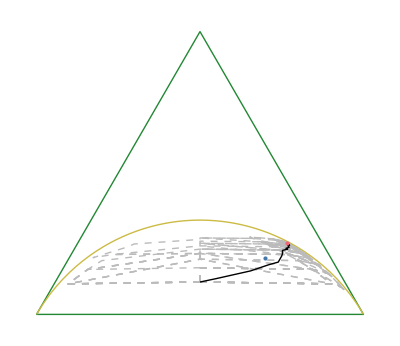

```mathematica
Show[Join[{triangle,parplot,Graphics[{purpleblue,PointSize[Medium],Point[finpoints.freq]}]},
Table[Graphics[{Dashed,Thin,grey,Line[T[finpoints.T[Table[upprob[sample,i],{i,0,nobs}]]]]}],{sample,nsamples}],{
Graphics@Line[T[finpoints.T[Table[upprob[i],{i,0,nobs}]]]],Graphics[{red,PointSize[Medium],Point[finpoints.upprob[nobs]]}]}]]
```

```mathematica
expdf0["overlearning1"]
```

overlearning1.pdf

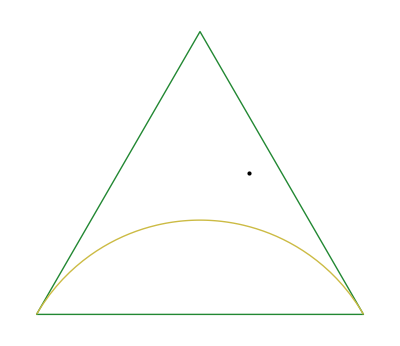

```mathematica
freq2={1/10,1-5/10,4/10};Show[{triangle,parplot,Graphics@Point[finpoints.freq2]}]
```

```mathematica
nobs2=15;data2=RandomChoice[freq2->{1,2,3},nobs2];
```

```mathematica
nsamples2=25;
updens2[0]=FS[(m-1)^4/Integrate[(m-1)^4,{m,0,2}]];
upprob2[0]=FS@NIntegrate[probm*updens2[0],{m,0,2}];
```

```mathematica
Do[
datas=RandomSample[data2];
updens2[sample,0]=updens2[0];
upprob2[sample,0]=upprob2[0];
Do[Print[sample," -",i];updens2[sample,i]=Assuming[0<m<2,FS[probm[[datas[[i]]]]*updens2[sample,i-1]/NIntegrate[probm[[datas[[i]]]]*updens2[sample,i-1],{m,0,2}]]];
upprob2[sample,i]=FS@NIntegrate[probm*updens2[sample,i],{m,0,2}],{i,1,nobs2}];,{sample,1,nsamples2}];
```

```mathematica
Do[upprob2[i]=Mean[Table[upprob2[sample,i],{sample,nsamples2}]],{i,nobs2}];{upprob2[nobs2],freq2}//N//MF
```

(0.13709 | 0.271276 | 0.591634
0.1 | 0.5 | 0.4)

```mathematica
Table[upprob2[samples,nobs2],{samples,8}]//MF
```

(0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634
0.13709 | 0.271276 | 0.591634)

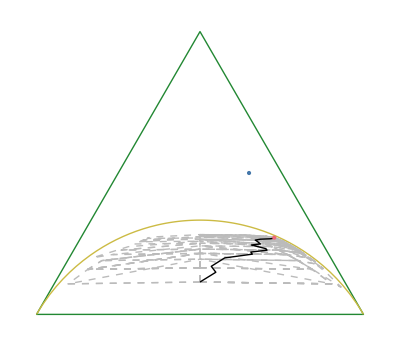

```mathematica
Show[Join[{triangle,parplot,Graphics[{purpleblue,PointSize[Medium],Point[finpoints.freq2]}]},
Table[Graphics[{Dashed,Thin,grey,Line[T[finpoints.T[Table[upprob2[sample,i],{i,0,nobs2}]]]]}],{sample,nsamples2}],{
Graphics@Line[T[finpoints.T[Table[upprob2[i],{i,0,nobs2}]]]],Graphics[{red,PointSize[Medium],Point[finpoints.upprob2[nobs2]]}]}]]
```

```mathematica
expdf0["overlearning2"]
```

overlearning2.pdf